```mathematica
ClearAll["Global`*"];
```

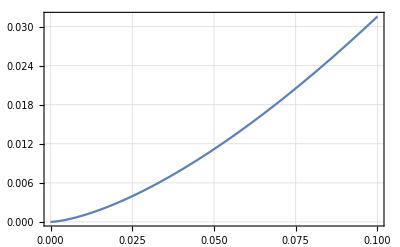

```mathematica
f[x_] = x^(1/2)*Sin[x]; a=0;b=0.1;eps=0.0001;
f1[x_] = Dt[f[x], {x, 1}];
f2[x_]=Dt[f[x],{x, 2}];
Plot[f[x], {x, a, b},Frame->True, GridLines->Automatic]
```

```mathematica
(*Для ручного просчёта*)
```

```mathematica
f4[x_]=Dt[f[x],{x, 4}]
```

(3 Cos[x])/(2 x^(5/2))-(2 Cos[x])/(√x)-(15 Sin[x])/(16 x^(7/2))+(3 Sin[x])/(2 x^(3/2))+√x Sin[x]

```mathematica
N[f4[0.1]]
```

174.476

```mathematica
(*Конец*)
```

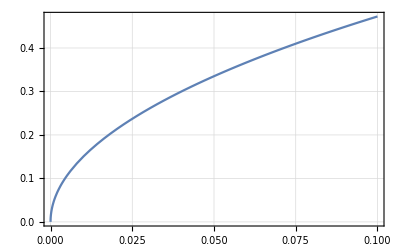

```mathematica
Plot[f1[x], {x, a, b},Frame->True, GridLines->Automatic]
```

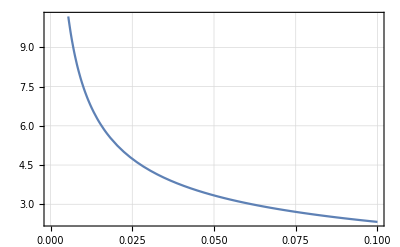

```mathematica
Plot[f2[x], {x, a, b},Frame->True, GridLines->Automatic]
```

```mathematica
(*Метод правых прямоугольников*)
```

```mathematica
Minimum = FindMaximum[{f2[x], a ≤ x ≤ b}, {x}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{7.41358,{x→0.0102303}}

```mathematica
(*для более точного результата нужно выбрать другой интервал (больше)*)
```

```mathematica
h=Sqrt[24*eps/((b-a)Minimum [[1]])]
```

0.0568973

```mathematica
n = Ceiling[(b-a)/h]
h=(b-a)/n
```

2

0.05

```mathematica
J=h*Sum[f[a+h*i], {i, 1, n}]
```

0.00213729

```mathematica
(*Рунге*)
```

```mathematica
J1 = (h/2)*Sum[f[a+(h/2)*i], {i, 1, n*2}]
```

0.00168046

```mathematica
r=J-J1
```

0.000456825

```mathematica
(*Погрешность по остаточному члену*)
```

```mathematica
R = h^4*(b-a)/2*f[a+0.1]
```

9.86566×10^-9

```mathematica
(*Метод Ньютона*)
```

(3 Cos[x])/(2 x^(5/2))-(2 Cos[x])/(√x)-(15 Sin[x])/(16 x^(7/2))+(3 Sin[x])/(2 x^(3/2))+√x Sin[x]

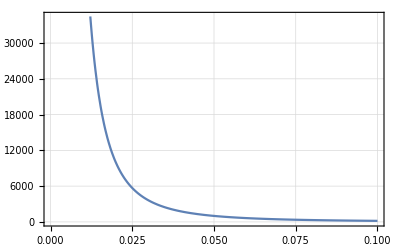

```mathematica
f4[x_]=Dt[f[x],{x, 4}]
Plot[f4[x], {x, a, b},Frame->True, GridLines->Automatic]
```

```mathematica
h=((80*0.001)/((b-a)*f4[a+0.1]))^(1/4)
n=Ceiling[(b-a)/h]
h = (b-a)/(3*n)
Jn = N[3*h/8*(f[a]+2*Sum[f[a+(3*i)*h], {i, 1, n- 1}] + 3*Sum[(f[a+(i*3-2)*h]+ f[a+(i*3-1)*h]) ,{i, 1, n}]+f[b] )]
```

0.260219

1

0.0333333

0.00126782

```mathematica
(*Погрешность по остаточному члену*)
```

```mathematica
R = h^4*(b-a)/80*f4[a+0.1]
```

2.69254×10^-7

```mathematica
(*оценим погрешность интеграла применяя правило Рунге*)
```

```mathematica
h2 = (((80*0.001)/((b-a)*f4[a+0.1]))^(1/4))/2
n2=Ceiling[(b-a)/h]
h2= (b-a)/(6*n)
Jn2 = N[3*h2/8*(f[a]+2*Sum[f[a+(3*i)*h2], {i, 1, n2- 1}] + 3*Sum[(f[a+(i*3-2)*h2]+ f[a+(i*3-1)*h2]) ,{i, 1, n2}]+f[b] )]
```

0.130109

3

0.0166667

0.00331476

```mathematica
r = Jn2 - Jn
```

0.00204693

```mathematica
(*Погрешность Экстраполяция Ричардсона*)
```

```mathematica
Jt=Integrate[f[x],{x,a,b}]
```

0.00126374

```mathematica
Jr = (4*Jn2 -Jn)/3
δ = Abs[Jr-Jt]/Jt
```

0.00399707

2.16289

```mathematica
(*Рекурентная формула Симпсона*)
M=7;
T[0]=0.5(b-a)*(f[a]+f[b]);
Do[h=(b-a)/(2^j);n=2^(j-1);T[j]=0.5*T[j-1]+h*Sum[f[a+(2k-1)*h],{k,n}],{j,1,M-1}];
Array[T,M,0]
δ=Abs[T[M-1]-Jt]/Jt
```

{0.0015785,0.00134804,0.00128584,0.00126945,0.0012652,0.00126411,0.00126383}

0.0000741218

```mathematica
Do[S[j]=(4*T[j]-T[j-1])/3,{j,1,M-1}]
Array[S,M-1,1]
```

{0.00127121,0.0012651,0.00126398,0.00126378,0.00126375,0.00126374}

```mathematica
Jt=Integrate[f[x],{x,a,b}]
```

0.00126374